### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={50,100,10}; (*мощности слоев*)
slopes = {0Degree, 0.5 Degree, 0.8 Degree, 0 Degree, -0.5 Degree} ;(*наклон слоев*)

len = 1000;(*длина профиля*)
dx = 10;(*шаг по профилю*)

type = -1 ;
listV = {1500,2500,3300,3500, 3500,3700}; (*набор скоростей *)
```

```mathematica
(*folding parametres *)
hDispersion = 1000;(*степень складчатости нижнего слоя в метрах*)
hTapering =10; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 5; (*start filter radius for GaussianFilter*)
```

```mathematica
velocityTrend = {3.5,0,3,2,1};(*1 or 0*)
velocityAnomaly ={0.5,0.2,0.04,0.06,0.08,0.1};
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "random"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
type =1;
horizons = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
table = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["table"]];
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"};
PlotDepthSection[horizons, optsDepth]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]];
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]];
```

```mathematica
PlotVelocity[velModel, horizons]
```

-Graphics-

```mathematica
data=Table[{x,Flatten[velModel[[All,25,All,4]],2][[x]]},{x,0,1600,1}];
ListLinePlot[data.RotationMatrix[Pi/2],AspectRatio->1.5, AxesLabel->{"v, m/s","h,m"},LabelStyle->Medium]
```

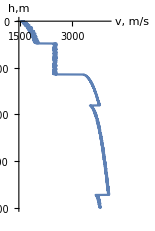

-Graphics-

```mathematica
velModelcopy=velModel
velModel[[2]]=Map[{#[[1]],#[[2]],#[[3]],#[[4]]+(30*Sin[0.2*#[[2]]/100])+20*Sin[0.1*#[[2]]/100]}&,velModel[[2]],{2}];
velModel[[3]]=Map[{#[[1]],#[[2]],#[[3]],#[[4]]+(30*Sin[0.1*#[[2]]/100])+20*Sin[0.05*#[[2]]/100]}&,velModel[[3]],{2}];
velModel[[4]]=Map[{#[[1]],#[[2]],#[[3]],#[[4]]+(30*Sin[0.05*#[[2]]/100])+20*Sin[0.025*#[[2]]/100]}&,velModel[[4]],{2}];
velModel[[5]]=Map[{#[[1]],#[[2]],#[[3]],#[[4]]+(50*Sin[0.025*#[[2]]/100])+50*Sin[0.0125*#[[2]]/100]}&,velModel[[5]],{2}];
velModel[[6]]=Map[{#[[1]],#[[2]],#[[3]],#[[4]]+(70*Sin[0.0125*#[[2]]/100])+70*Sin[0.00615*#[[2]]/100]}&,velModel[[6]],{2}];
velModel[[7]]=Map[{#[[1]],#[[2]],#[[3]],#[[4]]+(90*Sin[0.006125*#[[2]]/100])+90*Sin[0.003*#[[2]]/100]}&,velModel[[7]],{2}];
```

```mathematica
PlotVelocity[velModel, horizons]
```

-Graphics-

```mathematica
ListLinePlot[Table[{dx*x,velModel[[2,All,2,4]][[x]]},{x,0,100}], AxesOrigin->{0,1500}, AspectRatio->1/6,AxesLabel->{"x, m","v, m/s"}]
ListLinePlot[Table[{dx*x,velModel[[3,All,2,4]][[x]]},{x,0,100}], AxesOrigin->{0,1500}, AspectRatio->1/6,AxesLabel->{"x, m","v, m/s"}]
ListLinePlot[Table[{dx*x,velModel[[4,All,2,4]][[x]]},{x,0,100}], AxesOrigin->{0,1500}, AspectRatio->1/6,AxesLabel->{"x, m","v, m/s"}]
ListLinePlot[Table[{dx*x,velModel[[5,All,2,4]][[x]]},{x,0,100}], AxesOrigin->{0,1500}, AspectRatio->1/6,AxesLabel->{"x, m","v, m/s"}]
```

```mathematica
velModel[[5,All]]
```

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"};
PlotTimeSection[time, optsTime]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, "regular"][["dataset"]];
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]];
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},											
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

```mathematica
Clear[t];
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]];
```

{FittedModel[-32.5901+3552.49 t],FittedModel[-18.216+3550.43 t],FittedModel[59.8784+3233.94 t],FittedModel[42.7264+3755.55 t]}

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

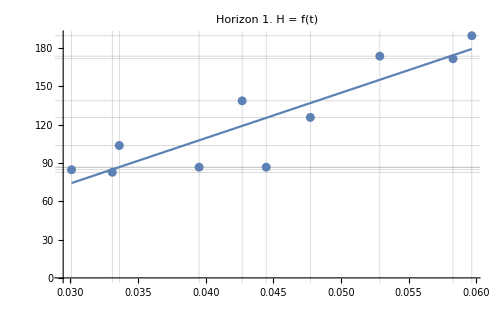
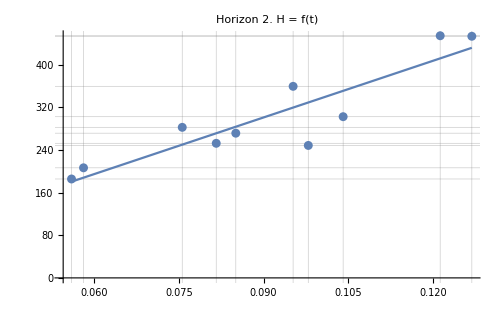
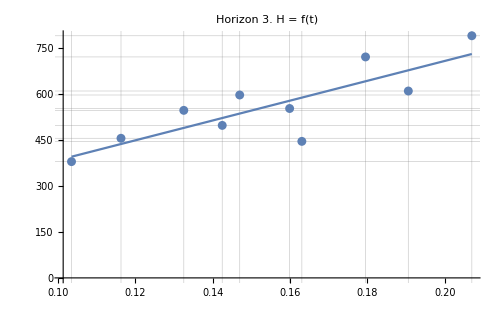
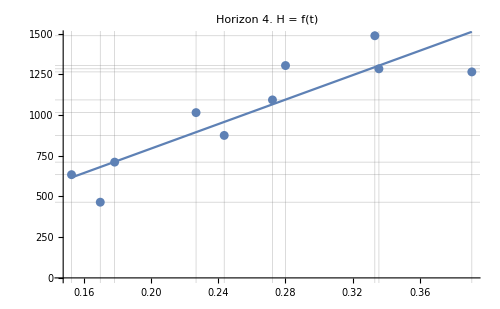

```mathematica
LinearRegressionPlots[wellValuesHT,lmSetHT, t, "H = f(t)", {"t, s","h, m"}]
```

### VTMethod

```mathematica
lmSetVT=VTMethod[wellDataset,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,time, t][["lmParametres"]];
wellValuesVT=VTMethod[wellDataset,time, t][["wellValues"]];
resultVT = VTMethod[wellDataset, time, t][["result"]];
fitsVT = VTMethod[wellDataset, time, t][["fits"]];
```

{FittedModel[2174.76+13794.1 t],FittedModel[3302.58+478.336 t],FittedModel[4121.02-3110.02 t],FittedModel[3810.23+395.052 t]}

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

General::stop: Further output of NumberForm::reqsigz will be suppressed during this calculation.

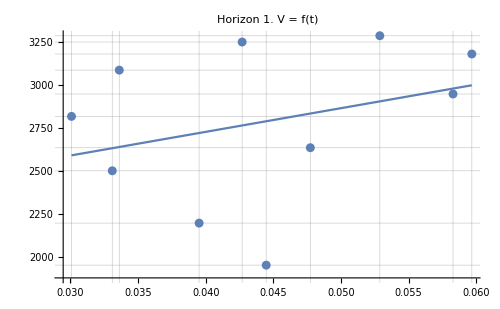
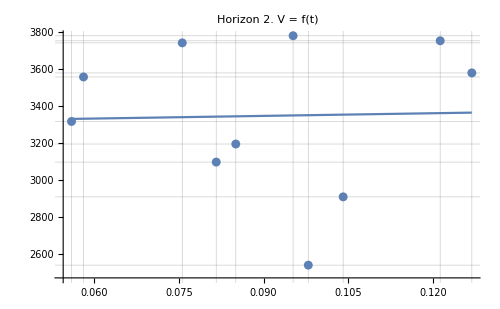
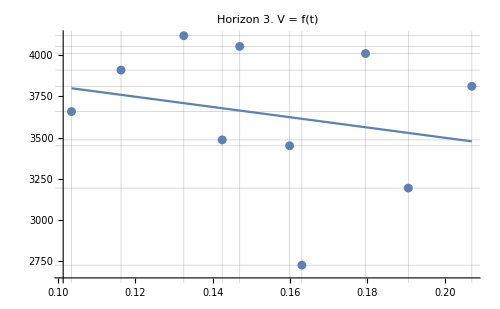
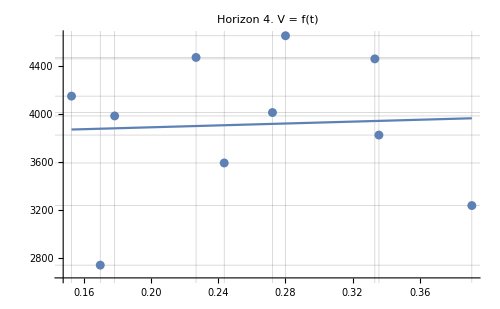

```mathematica
LinearRegressionPlots[wellValuesVT[[All, All,2;;3]],lmSetVT, t, "V = f(t)", {"t, s","v, m/s"}]
```

### THMethod

```mathematica
Clear[h];
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]];
resultTH=THMethod[wellDataset, time, h][["result"]];
```

{FittedModel[0.0165438+0.000222268 h],FittedModel[0.0209394+0.000229299 h],FittedModel[0.0339319+0.000215319 h],FittedModel[0.0450852+0.000210537 h]}

```mathematica
(*TimesBy[wellValuesTH[[All,All,2]],1000]
```

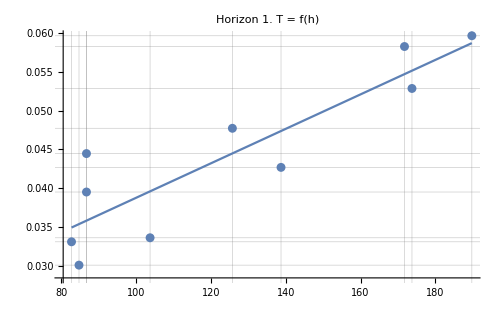
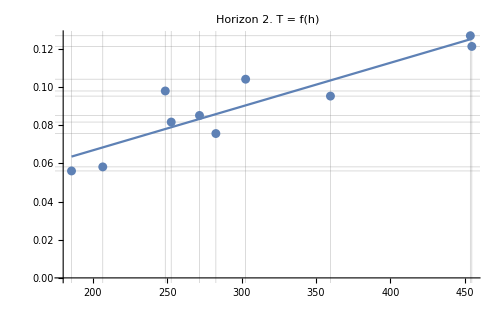
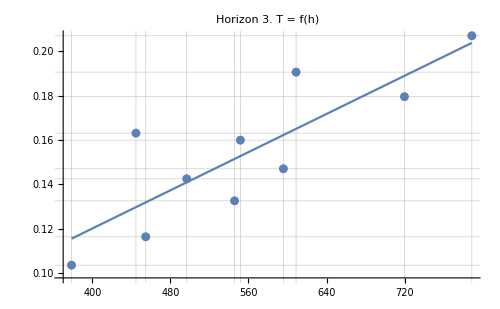
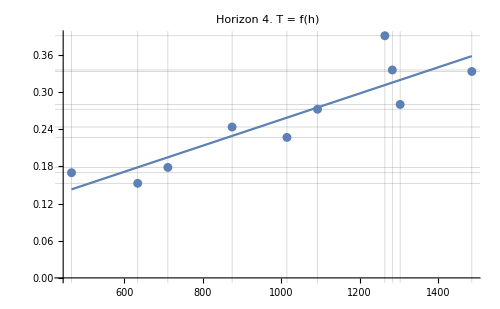

```mathematica
LinearRegressionPlots[wellValuesTH, lmSetTH, h, "T = f(h)", {"h, m","t, ms"}]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]];
fitsVave = VaveMethod[wellDataset, time][["fits"]];
```

{2784.49,3345.72,3641.47,3912.29}

### VaveVOGTMethod

```mathematica
Clear[v];
lmSetVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["lmSet"]]
lmParametresVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["lmParametres"]];
wellValuesVaveVOGT= VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["wellValues"]];
resultVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["result"]];
plotDataVaveVOGT=VaveVOGTMethod[wellDataset, horizons, time, vOGT, v][["plotData"]];
```

{FittedModel[3.92623×10^-12+0.740662 v],FittedModel[-2.94674×10^-11+1.10716 v],FittedModel[2.05096×10^-11+0.834269 v],FittedModel[1.83056×10^-11+0.719225 v]}

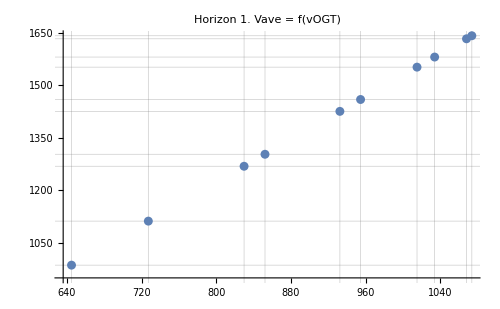
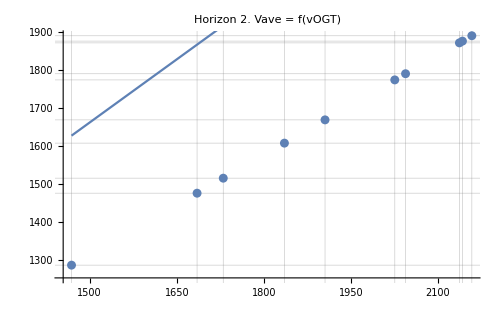
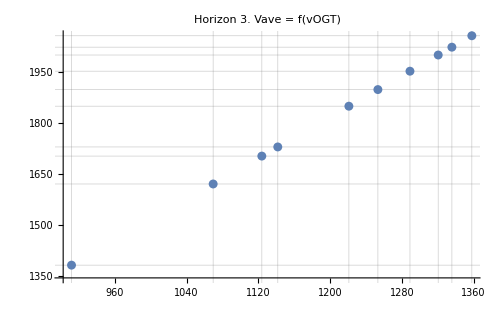
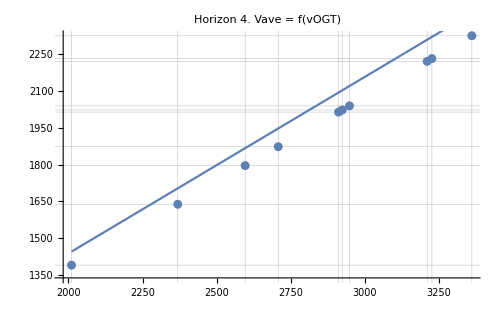

```mathematica
LinearRegressionPlots[plotDataVaveVOGT,lmSetVaveVOGT, vOGT, "Vave = f(vOGT)", {"vOGT, m/s","vAve, m/s"}]
```

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1600,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}, PlotLegends->{"H = f(t)"}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}, PlotLegends->{"V = f(t)"}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}, PlotLegends->{"T = f(h)"}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}, PlotLegends->{"Vave"}],
ListLinePlot[resultVaveVOGT[[2;;-1]], PlotStyle->{Yellow}, PlotLegends->{"Vave = f(vOGT)"}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVaveVOGT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "VaveVOGT"]
```

-Graphics-

```mathematica
RandomInteger[{1,10}]
```

7

$Aborted